# Arm state visualization

## Import

```mathematica
(*ClearAll["Global`*"]
Clear["Global`*"]*)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_04_13__13_03_05/"; 
figExpPath="~thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/Mathematica/";

SetDirectory[dirName];
all=Import["State.txt", "Table"];
varNames=all[[1]];
data = all[[2;;-2]];
numVars=Dimensions[varNames];
numData=Length[data]

fitXml = Import["GA_Progress.xml"];
fitness=Cases[fitXml,XMLElement["Generation",{_,"BestFitness"->fit_,_},___]->fit,Infinity];
fitness=ToExpression[fitness];
font="Arial";
```

## Fitness

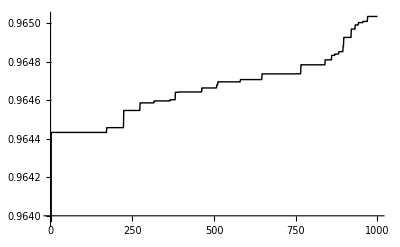

```mathematica
fitP =ListLinePlot[fitness[[1;;Length[fitness]]],PlotStyle->Black,PlotRange->Automatic,ImageSize->400]
maxFit = Max[fitness]
```